```mathematica
ClearAll["Global`*"];
{b[1],b[2],b[3]}={√α,√β,√γ};b[0]=b[3];
h=Cos[2θ]^2 Sin[2θ];
Do[λ[m][u_]=({{0, b[m]^2 u^2, b[m]^2 b[m-1]^2 u^4}, {1, 0, 0}, {0, 1, 0}});ν[m][u_]=({{1, 0, -u^2 b[m]^2}, {1, 0, 0}, {0, 1, 0}});
Mat=ConstantArray[0,{12,12}];
Mat [[ 4;;12,4;;12]]=KroneckerProduct[ν[m][u],ν[m][u]];
Mat [[1;;3,1;;3]]=λ[m][u];
Mat [[1;;3,4;;12]]=({{4, 0, 0, 0, 0, 0, -8 u b[m](1-b[m]/b[m-1])h, -8 u b[m]^2/b[m-1] h, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}});
mat[m][u_]=Mat;
,{m,1,3}];
λλ[u_]=λ[3][u].λ[2][u].λ[1][u];
νν[u_]=ν[3][u].ν[2][u].ν[1][u];
MAT[u_]=mat[3][u].mat[2][u].mat[1][u];
Nk[u_]:=(
vλ=Eigenvectors[λλ[u]]//Transpose//Inverse;
vν=Eigenvectors[νν[u]]//Transpose//Inverse;
V=ConstantArray[0,{12,12}];
V[[1;;3,1;;3]]=vλ;
V[[4;;12,4;;12]]=KroneckerProduct[vν,vν];
MATmrotated=V.MAT[-u].Inverse[V]//Chop;
MATprotated=V.MAT[u].Inverse[V]//Chop;
Λ=Eigenvalues[λλ[u]][[1]]//Chop;
list=Position[MATmrotated//Diagonal,x_/;Abs[x/Λ-1.]<0.0001]//Flatten;(*this gives the basis vectors associated with eigenvalue Λ*)
mp=1/Λ MATprotated [[list,list]]//Chop;
mm=1/Λ MATmrotated [[list,list]]//Chop;
nk=((mm [[1,2]]+mm [[1,3]])-(mp [[ 1,2]]+mp [[1,3]]))/((mp [[1,2]]+mp [[1,3]])+(mm [[1,2]]+mm [[1,3]]))//Chop;
Return[nk]
);
```

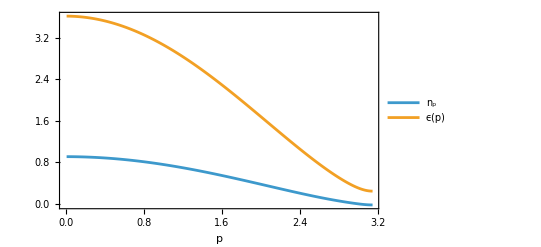

```mathematica
{α,β,γ}={1.,2.,3.};θ=π/8;
B[p_]=(3^(1/3) α β+3^(1/3) α γ+3^(1/3) β γ+(9 α β γ Cos[p]+1/3 √(-27 (β γ+α (β+γ))^3+729 α^2 β^2 γ^2 Cos[p]^2))^(2/3))/(3^(2/3) (9 α β γ Cos[p]+1/3 √(-27 (β γ+α (β+γ))^3+729 α^2 β^2 γ^2 Cos[p]^2))^(1/3));(*solution of : Solve[B^2-2 α β γ B^-1 Cos[p]==α β+β γ+α γ,B]//Simplify*)
ϵofp[p_]=√(((B[p]^2-α β)(B[p]^2-α γ)(B[p]^2-β γ))/(α β γ B[p]^2));
Show[ListLinePlot[{Table[{p,Nk[1/ϵofp[p]]},{p,0.01,π,0.01}],Table[{p,ϵofp[p]},{p,0.01,π,0.01}]},PlotRange->All,PlotLegends->{"n_p","ϵ(p)"}],Frame->True,FrameLabel->{{"",""},{"p",""}}]
```

```mathematica
ClearAll["Global`*"];

$Assumptions=Element[{u,eps,alpha,beta,gamma,q,rho,h},Reals]&&alpha>0&&beta>0&&gamma>0&&eps>0;

(*Period-three couplings*)
b[1]=Sqrt[alpha];
b[2]=Sqrt[beta];
b[3]=Sqrt[gamma];

(*Periodic convention inside one three-site cell*)
b[0]=b[3];

s1=alpha+beta+gamma;
s2=alpha beta+alpha gamma+beta gamma;
s3=alpha beta gamma;
```

```mathematica
ClearAll[nu,lam];

nu[m_][u_]:={{1,0,-u^2 b[m]^2},{1,0,0},{0,1,0}};

lam[sgn_][m_][u_]:={{0,sgn u^2 b[m]^2,sgn u^4 b[m]^2 b[m-1]^2},{1,0,0},{0,1,0}};

Ncell[u_]:=FullSimplify[nu[3][u].nu[2][u].nu[1][u]];

Lcell[sgn_][u_]:=FullSimplify[lam[sgn][3][u].lam[sgn][2][u].lam[sgn][1][u]];

Print["Ncell ="];
MatrixForm[Ncell[u]]

Print["Lcell positive ="];
MatrixForm[Lcell[+1][u]]

Print["Lcell negative ="];
MatrixForm[Lcell[-1][u]]
```

Ncell =

(1-gamma u^2 | -beta u^2 | -alpha u^2
1 | -beta u^2 | -alpha u^2
1 | 0 | -alpha u^2)

Lcell positive =

(beta gamma u^4 | alpha gamma u^4 | alpha gamma^2 u^6
beta u^2 | alpha beta u^4 | 0
0 | alpha u^2 | alpha gamma u^4)

Lcell negative =

(-beta gamma u^4 | alpha gamma u^4 | alpha gamma^2 u^6
-beta u^2 | -alpha beta u^4 | 0
0 | -alpha u^2 | -alpha gamma u^4)

```mathematica
charN=FullSimplify[CharacteristicPolynomial[Ncell[u],rho]];

expectedCharN=rho^3+(-1+u^2 s1) rho^2+u^4 s2 rho+u^6 s3;

Print["charN - expectedCharN ="];
FullSimplify[charN-expectedCharN]
```

charN - expectedCharN =

-2 (rho^3+(beta gamma+alpha (beta+gamma)) rho u^4+alpha beta gamma u^6+rho^2 (-1+(alpha+beta+gamma) u^2))